```mathematica
leqn=Laplacian[u[x,y],{x,y}]==0;
```

```mathematica
Ω=Annulus[{0,0},{3,10},{0,2π}];
```

```mathematica
innerCond=DirichletCondition[u[x,y]== 10,Norm[{x,y}]==3];
outerCond=DirichletCondition[u[x,y]== 0,Norm[{x,y}]==10];
```

```mathematica
sol=NDSolve[{leqn,innerCond, outerCond},u[x,y],{x,y}∈Ω];
```

```mathematica
Plot3D[Evaluate[u[x,y]/.sol⟦1⟧],{x,y}∈Ω,PlotStyle->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
u[x,y]/.sol[[1]];
```

```mathematica
InterpolatingFunction[…][x,y];
```

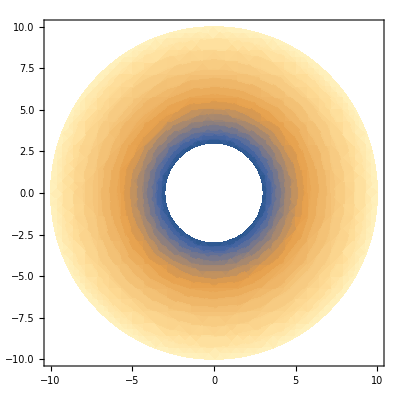

```mathematica
DensityPlot[%224,{x,-10.000000000000068,10.000000000000071},{y,-10.000000000000068,10.000000000000068},Mesh->Automatic,MeshFunctions->{#3&}]
```